### Categorization

Tutorial

NounouM2

NounouM2`

NounouM2/tutorial/Load MiCam images (.GSD) and plot

### Keywords

Details

# Load MiCam images (.GSD) and plot

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

XXXX.

Initialize Package

```mathematica
<<NounouM2`
```

Welcome to NounouM2, the Mathematica interface to nounou!

( last updated:  Mon 3 Mar 2014 15:11:27 )

( current Git HEAD:  c1b623a1c1f703ddee3ec7367c20c50915fc6ff2 )

( http://github.org/ktakagaki/nounoum )

<<Set JLink` java stack size to 6144Mb>>

```mathematica
(*This will allow one to see logging traces and errors*)
(*On windows, the content of these logs will be output to the default user directory as a text file*)
ShowJavaConsole[]
```

«JavaObject[com.wolfram.jlink.ui.ConsoleWindow]»

Load Data Files

```mathematica
nnDataDirectory = "E:\\data\\Micam\\dc-stimulation\\140224"
```

E:\data\Micam\dc-stimulation\140224

```mathematica
(*The $NNReader object is initialized by default upon calling <<NounouM2`*)
(*The object starts out empty*)
(*Further reader objects can be created, using the Java constructor, but beware of having too many readers with too many open data files---and running out of memory*)
$NNReader@load[nnDataDirectory<>"\\mag140224006A.gsd"]
```

Java::excptn: A Java exception occurred: "java.lang.OutOfMemoryError: Java heap space\n\tat java.lang.Integer.valueOf(Integer.java:585)\n\tat scala.runtime.BoxesRunTime.boxToInteger(BoxesRunTime.java:70)\n\tat scala.collection.mutable.WrappedArray$ofInt.apply(Wr" … "o.FileAdapter$class.load(FileAdapter.scala:56)\n\tat nounou.data.io.FileAdapterGSDGSH$.load(FileAdapterGSDGSH.scala:13)\n\tat nounou.DataReader.load(DataReader.scala:187)\n\tat nounou.DataReader.load(DataReader.scala:196)".

$Failed

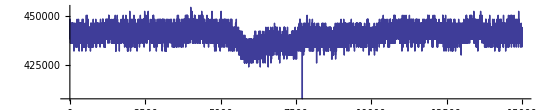

```mathematica
ListLinePlot[$NNReader@data[]@readTraceAbsA[62*92+42-1, NN`frameRangeAll[]],PlotRange->All, AspectRatio->1/5, ImageSize->72*8]
```

```mathematica
ListLinePlot[$NNReader@dataORI[]@readTraceAbsA[62*92+42-1, NN`frameRangeAll[]],PlotRange->All, AspectRatio->1/5, ImageSize->72*8]
```

Java::excptn: A Java exception occurred: "java.lang.IndexOutOfBoundsException: 0\n\tat scala.collection.immutable.Vector.checkRangeConvert(Vector.scala:137)\n\tat scala.collection.immutable.Vector.apply(Vector.scala:127)\n\tat nounou.data.traits.XFrames$class.isRealisticFrameRange(XFrames.scala:61)\n\tat nounou.data.XData.isRealisticFrameRange(XData.scala:13)\n\tat nounou.data.XData.readTrace(XData.scala:104)\n\tat nounou.data.XData.readTrace(XData.scala:98)\n\tat nounou.data.XData.readTraceAbsA(XData.scala:149)".

ListLinePlot::lpn: $Failed is not a list of numbers or pairs of numbers.

ListLinePlot[$Failed,PlotRange→All,AspectRatio→1/5,ImageSize→576]

```mathematica
$NNReader@header[]@toStringFull[]
```

XHeader: Map(AUXnChNext -> 0, AUXnChanum -> 2, AUXnDummy1 -> 512, AUXnDummy2 -> 1, AUXnDummy3 -> 0, AUXnFrameSize -> 15000, AUXnOfset -> 0, AUXnRate -> 20, AUXnShift -> 1, AUXnTimeNext -> 0, dAverage -> 1.0, dDummy -> 9.1837E-41, dOrgSampleTime -> 0.6, dSampleTime -> 0.6, nDataXsize -> 92, nDataYsize -> 80, nDummy -> 0, nFrameSize -> 15000, nImgXsize -> 92, nImgYsize -> 80, nLeftSkip -> 0, nOrgFrmSize -> 15000, nOrgImgXsize -> 92, nOrgImgYsize -> 80, nShift -> 1, nTopSkip -> 0)

```mathematica
$NNReader@toStringChain[]
```

DataReader LOADED DATA SUMMARY
================================
DataReader( data ch:0, dataAux ch:0, mask: XMask: 0 _masks, events: 0)

     [header  ] XHeaderNull
     [dataORI ] XDataFilterHolder: XDataNull()     
          \ XDataFilterDecimate: off (factor=1)     
               \ XDataFilterBuffer: bufferPageLength=16384, garbageQueBound=1024     
                    \ XDataFilterStatistics: 
                    \ XDataFilterFIR: kernel null (off)     
                         \ XDataFilterRMS: off (halfWindow=0)
                    \ XDataFilterFIR: kernel null (off)
                    \ XDataFilterMinMaxAbs: off (halfWindow=0)
     [dataAux ] XDataFilterHolder: XDataNull()     
          \ XDataFilterDecimate: off (factor=1)     
               \ XDataFilterBuffer: bufferPageLength=16384, garbageQueBound=1024     
                    \ XDataFilterStatistics: 
                    \ XDataFilterFIR: kernel null (off)     
                         \ XDataFilterRMS: off (halfWindow=0)
                    \ XDataFilterFIR: kernel null (off)
                    \ XDataFilterMinMaxAbs: off (halfWindow=0)
     [mask    ] XMask: 0 _masks
     [events  ] XEventsNull
     [spikes  ] XSpikesNull

More About

Related Tutorials

Related Wolfram Education Group Courses